```mathematica
Quit[]
```

First Example

```mathematica
data=TimeSeriesResample[TimeSeries[FinancialData["MSFT","Jan. 1, 2000"]],"BusinessDay"]//Normal;
```

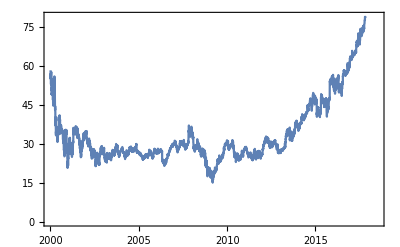

```mathematica
DateListPlot[data]
```

```mathematica
Length[data]
```

4648

```mathematica
values=data[[All,2]];keysp=Partition[values,10,1];valuesp = values[[11;;]];
```

```mathematica
Length@valuesp
```

4638

```mathematica
threaddata=Thread[Table[ArrayReshape[keysp[[i]],{1,10}]->valuesp[[i]],{i,1,Length@valuesp}]];
```

```mathematica
threaddata[[1]]
```

{{58.282,55.7812,56.907,55.,55.719,56.125,54.688,52.907,53.907,56.125}}→57.657

```mathematica
{trainingdata,testdata}=TakeDrop[threaddata,3500];
```

### Feed Forward

```mathematica
SNNnetRegression[dropoutrate_,nhidden_,nlayers_]:=NetChain[
Append[
Flatten@Table[{LinearLayer[nhidden],
ElementwiseLayer["SELU"],
DropoutLayer[dropoutrate,"Method"->"AlphaDropout"]}
,nlayers-1],
LinearLayer[]]];
net=SNNnetRegression[0.01,400,4]
```

NetChain[<>]

```mathematica
extractor=FeatureExtraction[N@Keys[trainingdata],"StandardizedVector"];
```

```mathematica
trainingdata[[1]]
```

{{58.282,55.7812,56.907,55.,55.719,56.125,54.688,52.907,53.907,56.125}}→57.657

```mathematica
extractor[Keys[trainingdata[[1]]]]
```

{6.03784,5.56038,5.81244,5.44931,5.61889,5.72666,5.45514,5.10732,5.33386,5.81822}

```mathematica
trainStandardized=Thread[Table[extractor[Keys[trainingdata[[i]]]],{i,1,Length@trainingdata}]->Table[Values[trainingdata[[i]]],{i,1,Length@trainingdata}]];
```

```mathematica
Mean[Keys@trainStandardized]
```

{-1.1342×10^-15,-5.49148×10^-16,-6.36951×10^-16,-6.88211×10^-16,4.98712×10^-16,-4.9129×10^-16,-9.39693×10^-16,-1.69261×10^-16,1.72307×10^-16,-9.15585×10^-16}

```mathematica
{trainedNet,lowestVal}=NetTrain[net,trainStandardized,{"TrainedNet","LowestValidationLoss"},ValidationSet->Scaled[0.1],MaxTrainingRounds->500,Method->"ADAM"]
```

{NetChain[<>],0.486332}

```mathematica
AssociationMap[ PredictorMeasurements[
Predict[trainingdata,Method->#,PerformanceGoal->"Quality"],testdata, "MeanSquare"]&,{"RandomForest", "DecisionTree", "GradientBoostedTrees", "NearestNeighbors","LinearRegression","GaussianProcess"}]
```

<|RandomForest→309.786,DecisionTree→301.441,GradientBoostedTrees→306.811,NearestNeighbors→286.063,LinearRegression→0.941704,GaussianProcess→891.021|>

```mathematica
RandomSeed[1234];RandomSample[testdata,2]
```

{{{50.79,50.48,52.29,51.79,52.17,51.22,52.055,55.09,54.71,53.}}→52.16,{{45.48,46.24,46.39,45.92,47.13,47.18,47.01,42.66,41.19,42.01}}→40.4}

```mathematica
trainedNet[extractor[{{45.47999954223633,46.2400016784668,46.38999938964844,45.91999816894531,47.130001068115234,47.18000030517578,47.0099983215332,42.65999984741211,41.189998626708984,42.0099983215332}}]]
```

43.6015

```mathematica
trainedNet[extractor[{{50.790000915527344,50.47999954223633,52.290000915527344,51.790000915527344,52.16999816894531,51.220001220703125,52.05500030517578,55.09000015258789,54.709999084472656,53.}}]]
```

53.6224

### RNN (seq 10)

```mathematica
rnn=NetChain[{GatedRecurrentLayer[32,"Dropout"->{"VariationalInput"->0.3},"Input"->{"Varying",10}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],GatedRecurrentLayer[128,"Dropout"->{"VariationalInput"->0.3}],SequenceLastLayer[],LinearLayer[128],Ramp,LinearLayer[1]},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
{trainedNet,lowestVal}= NetTrain[rnn,trainingdata,{"TrainedNet","LowestValidationLoss"},ValidationSet->Scaled[0.05],Method-> "ADAM",MaxTrainingRounds->100]
```

{NetChain[<>],15.3201}

```mathematica
trainedNet[trainingdata[[2,1]]]
```

28.9909

```mathematica
tvalues=Table[trainedNet[testdata[[i,1]]],{i,1,Length@testdata}];
```

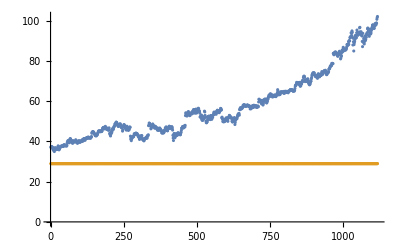

```mathematica
ListPlot[{testdata[[All,2]],tvalues}]
```

WindData

### RNN (seq 10)

```mathematica
Quit[]
```

```mathematica
wndData=TimeSeries[…];
```

```mathematica
DateListPlot[wndData]
```

-Graphics-

```mathematica
data=loadTimeSeriesResampled//Normal;
```

```mathematica
values=QuantityMagnitude@data[[All,2]];keysp=Partition[values,10,1];valuesp = values[[11;;]];
```

```mathematica
threaddata=Thread[Table[ArrayReshape[keysp[[i]],{1,10}]->valuesp[[i]],{i,1,Length@valuesp}]];
```

```mathematica
Length@data
```

58680

```mathematica
Length@threaddata
```

225491

```mathematica
{trainingdata,testdata}=TakeDrop[threaddata,45000];
```

```mathematica
rnn=NetChain[{GatedRecurrentLayer[32,"Dropout"->{"VariationalInput"->0.3},"Input"->{"Varying",10}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],SequenceLastLayer[],LinearLayer[128],Ramp,LinearLayer[1]},"Output"->"Scalar"]
```

NetChain[<>]

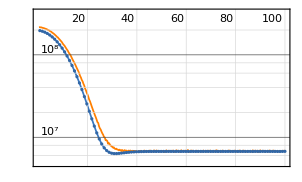
NetTrain Results
summary | ,,  batches:5700  rounds:100  time:6.1min  examples/s:12519
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:6.79×10^6
validation | ,,  loss:6.75×10^6
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
trinednet =  NetTrain[rnn,trainingdata,All,ValidationSet->testdata,BatchSize->800,Method-> "ADAM",MaxTrainingRounds->100]
```

```mathematica
AssociationMap[ PredictorMeasurements[
Predict[trainingdata,Method->#,PerformanceGoal->"DirectTraining"],testdata, "MeanSquare"]&,{"RandomForest"}]
```

<|RandomForest→367478.|>

```mathematica
SeedRandom[111];rsample=RandomSample[testdata,2]
```

{{{15571.1,15650.6,15550.,15302.7,15084.7,15006.5,15040.4,15374.6,15861.4,16102.7}}→16253.8,{{11153.3,10788.,10716.,10766.8,11116.3,11535.6,12580.1,13398.4,13455.7,13345.3}}→13460.6}

```mathematica
trainedNet[rsample[[1,1]]]
```

trainedNet[{{15571.1,15650.6,15550.,15302.7,15084.7,15006.5,15040.4,15374.6,15861.4,16102.7}}]

```mathematica
trainedNet[rsample[[2,1]]]
```

trainedNet[{{11153.3,10788.,10716.,10766.8,11116.3,11535.6,12580.1,13398.4,13455.7,13345.3}}]

```mathematica
tvalues=Table[trainedNet[testdata[[i,1]]],{i,1,Length@testdata}]
```

{trainedNet[{{13430.2,11922.1,12288.2,11877.9,11828.,11865.4,11913.5,12795.4,14132.3,14628.5}}],trainedNet[{{11922.1,12288.2,11877.9,11828.,11865.4,11913.5,12795.4,14132.3,14628.5,14886.8}}],trainedNet[{{12288.2,11877.9,11828.,11865.4,11913.5,12795.4,14132.3,14628.5,14886.8,14916.1}}],13665,trainedNet[{{11279.6,11370.,11467.,11703.2,12140.8,12811.6,13519.9,13896.4,13691.6,13421.6}}],trainedNet[{{11370.,11467.,11703.2,12140.8,12811.6,13519.9,13896.4,13691.6,13421.6,13012.8}}]}
 |  |  |  |

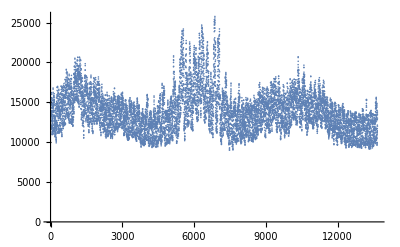

```mathematica
ListPlot[{testdata[[All,2]],tvalues}]
```

```mathematica
sobj=NetStateObject[trainedNet]
```

NetStateObject::arg1: First argument to NetStateObject should be a valid net.

$Failed

```mathematica
NestList[sobj[{#}]&,testdata[[1,1]],8]
```

NetStateObject::invindata1: Data supplied to port "Input" was a 1×1 matrix, but expected a n×10 matrix.

NetStateObject::invindata2: Data supplied to port "Input" was not a n×10 matrix.

General::stop: Further output of NetStateObject::invindata2 will be suppressed during this calculation.

{{{29.52,29.808,30.096,30.384,30.672,30.96,31.248,31.536,31.824,32.112}},{29.6887},$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
results=Union@Flatten@NestList[Drop[Join[#,{trainedNet[#]}],1]&,testdata[[1,1]],100]
```

{29.52,29.808,30.096,30.384,30.672,30.96,31.248,31.536,31.824,32.112,32.4739,32.7695,33.0625,33.3513,33.6347,33.9169,34.1959,34.4704,34.7422,35.0063,35.2681,35.5172,35.7594,35.9947,36.2229,36.4441,36.6581,36.8644,37.0634,37.2544,37.438,37.6135,37.7817,37.9425,38.0962,38.243,38.3828,38.5159,38.6426,38.7628,38.877,38.9853,39.0879,39.1851,39.277,39.364,39.4461,39.5237,39.5969,39.666,39.7311,39.7925,39.8502,39.9046,39.9558,40.004,40.0492,40.0918,40.1318,40.1693,40.2046,40.2377,40.2687,40.2979,40.3252,40.3509,40.375,40.3975,40.4187,40.4385,40.457,40.4744,40.4907,40.506,40.5203,40.5337,40.5462,40.5579,40.5689,40.5792,40.5888,40.5979,40.6063,40.6142,40.6216,40.6285,40.635,40.641,40.6467,40.652,40.6569,40.6616,40.6659,40.67,40.6737,40.6773,40.6806,40.6837,40.6866,40.6893,40.6919,40.6943,40.6965,40.6986,40.7005,40.7023,40.704,40.7056,40.7071,40.7085}

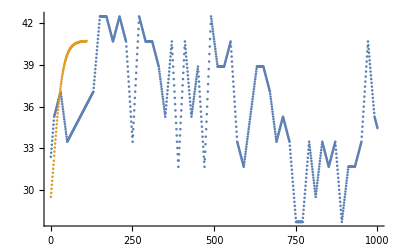

```mathematica
ListPlot[{testdata[[1;;1000,2]],results}]
```

### RNN (seq 100)

```mathematica
wndData=TimeSeriesResample[TimeSeries[WeatherData[GeoPosition[Entity["Company","AltaWindEnergyCenter::4h269"]], "WindSpeed",{{2018,1,1},Date[]}],MissingDataMethod->Automatic]]
```

TemporalData[TimeSeries, <<1>>]

```mathematica
DateListPlot[wndData]
```

-Graphics-

```mathematica
data=wndData//Normal;
```

```mathematica
values=QuantityMagnitude@data[[All,2]];keysp=Partition[values,100,1];valuesp = values[[101;;]];
```

```mathematica
threaddata=Thread[Table[keysp[[i]]->valuesp[[i]],{i,1,Length@valuesp}]];
```

```mathematica
Length@data
```

224061

```mathematica
{trainingdata,testdata}=TakeDrop[threaddata,200000];
```

```mathematica
rnn=NetChain[{ReshapeLayer[{1,100}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3},"Input"->{1,100}],GatedRecurrentLayer[128,"Dropout"->{"VariationalInput"->0.3}],GatedRecurrentLayer[128,"Dropout"->{"VariationalInput"->0.3}],SequenceLastLayer[],LinearLayer[256],Ramp,LinearLayer[1]},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
{trainedNet,lowestVal}= NetTrain[rnn,trainingdata,{"TrainedNet","LowestValidationLoss"},ValidationSet->testdata,BatchSize->500,Method-> "ADAM",MaxTrainingRounds->100]
```

{NetChain[<>],7.18641}

```mathematica
AssociationMap[ PredictorMeasurements[
Predict[trainingdata,Method->#,PerformanceGoal->"DirectTraining"],testdata, "MeanSquare"]&,{"RandomForest"}]
```

<|RandomForest→0.0582691|>

```mathematica
SeedRandom[111];rsample=RandomSample[testdata,2]
```

{{25.92,25.452,24.984,24.516,24.048,23.58,23.112,22.644,22.176,21.708,21.24,20.772,20.304,19.836,19.368,18.9,18.432,17.964,17.496,17.028,16.56,16.938,17.316,17.694,18.072,18.45,18.828,19.206,19.584,19.962,20.34,20.718,21.096,21.474,21.852,22.23,22.608,22.986,23.364,23.742,24.12,23.94,23.76,23.58,23.4,23.22,23.04,22.86,22.68,22.5,22.32,22.14,21.96,21.78,21.6,21.42,21.24,21.06,20.88,20.7,20.52,20.7,20.88,21.06,21.24,21.42,21.6,21.78,21.96,22.14,22.32,22.5,22.68,22.86,23.04,23.22,23.4,23.58,23.76,23.94,24.12,24.21,24.3,24.39,24.48,24.57,24.66,24.75,24.84,24.93,25.02,25.11,25.2,25.29,25.38,25.47,25.56,25.65,25.74,25.83}→25.92,{33.084,33.282,33.48,33.39,33.3,33.21,33.12,33.03,32.94,32.85,32.76,32.67,32.58,32.49,32.4,32.31,32.22,32.13,32.04,31.95,31.86,31.77,31.68,31.392,31.104,30.816,30.528,30.24,29.952,29.664,29.376,29.088,28.8,28.512,28.224,27.936,27.648,27.36,27.072,26.784,26.496,26.208,25.92,26.1,26.28,26.46,26.64,26.82,27.,27.18,27.36,27.54,27.72,27.9,28.08,28.26,28.44,28.62,28.8,28.98,29.16,29.34,29.52,29.43,29.34,29.25,29.16,29.07,28.98,28.89,28.8,28.71,28.62,28.53,28.44,28.35,28.26,28.17,28.08,27.99,27.9,27.81,27.72,27.72,27.72,27.72,27.72,27.72,27.72,27.72,27.72,27.72,27.72,27.72,27.72,27.72,27.72,27.72,27.72,27.72}→27.72}

```mathematica
trainedNet[rsample[[1,1]]]
```

26.3141

```mathematica
trainedNet[rsample[[2,1]]]
```

28.8203

```mathematica
tvalues=Table[trainedNet[testdata[[i,1]]],{i,1,Length@testdata}]
```

{35.4402,35.431,35.4195,35.4038,35.3985,35.3976,35.3983,35.4294,35.459,35.4863,35.5209,35.5495,35.587,35.6225,35.6409,35.6363,35.6465,35.6756,35.7193,35.7861,35.8497,35.9291,36.0063,36.0838,23914,13.5461,13.7582,13.7979,13.7951,13.8435,14.1146,14.6878,15.3085,15.9409,16.444,16.6839,16.8454,17.0185,17.2092,17.3822,17.5195,17.7099,17.9179,18.2364,18.7657,19.6799,20.2221,20.7081}
 |  |  |  |

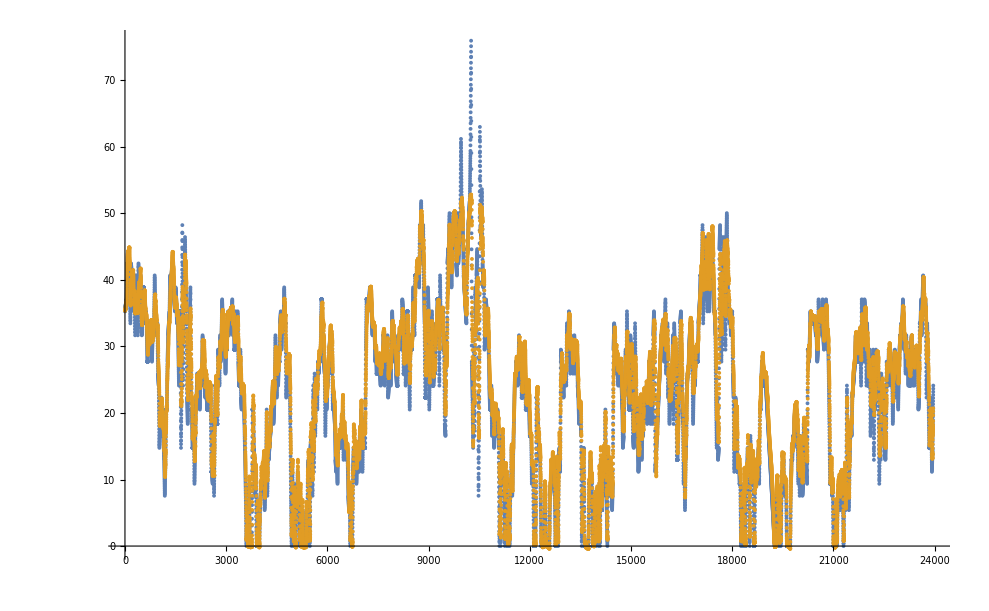

```mathematica
ListPlot[{testdata[[All,2]],tvalues}]
```

```mathematica
results=NestList[Drop[Join[#,{trainedNet[#]}],1]&,testdata[[1,1]],100];
```

### RNN + CNN

```mathematica
Quit[]
```

```mathematica
(*wndData=TimeSeries[…];*)
```

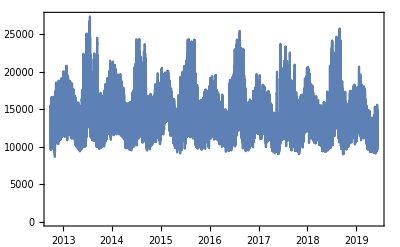

```mathematica
DateListPlot[loadTimeSeriesResampled]
```

```mathematica
data=loadTimeSeriesResampled//Normal;
```

```mathematica
values=QuantityMagnitude@data[[All,2]];keysp=Partition[values,10,1];valuesp = values[[11;;]];
```

```mathematica
threaddata=Thread[Table[ArrayReshape[keysp[[i]],{1,10}]->valuesp[[i]],{i,1,Length@valuesp}]];
```

```mathematica
Length@data
```

58680

```mathematica
Length@threaddata
```

58670

```mathematica
{trainingdata,testdata}=TakeDrop[threaddata,45000];
```

```mathematica
rnn=NetChain[
{ConvolutionLayer[100,6,"Interleaving"->True],
Ramp,
ConvolutionLayer[100,6,"Interleaving"->True],
Ramp,
ConvolutionLayer[10,6,"Interleaving"->True],
Ramp,
GatedRecurrentLayer[32,"Dropout"->{"VariationalInput"->0.3},"Input"->{"Varying",10}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],SequenceLastLayer[],LinearLayer[128],Ramp,LinearLayer[1]},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
{trainedNet,lowestVal}= NetTrain[rnn,trainingdata,All,ValidationSet->testdata,BatchSize->800,Method-> "ADAM",MaxTrainingRounds->100]
```

NetTrain::nettinf1: Could not automatically infer types for input and outputs of partially specified net NetChain[«13»]. Please specify shapes for the input and/or output ports of the net before calling NetTrain.

NetTrain::nfspec: Cannot train net: parameter "KernelSize" of first layer is not fully specified.

Set::shape: Lists {trainedNet,lowestVal} and $Failed are not the same shape.

$Failed

```mathematica
AssociationMap[ PredictorMeasurements[
Predict[trainingdata,Method->#,PerformanceGoal->"DirectTraining"],testdata, "MeanSquare"]&,{"RandomForest"}]
```

<|RandomForest→0.0521153|>

```mathematica
SeedRandom[111];rsample=RandomSample[testdata,2]
```

{{{25.92,25.452,24.984,24.516,24.048,23.58,23.112,22.644,22.176,21.708}}→21.24,{{33.084,33.282,33.48,33.39,33.3,33.21,33.12,33.03,32.94,32.85}}→32.76}

```mathematica
trainedNet[rsample[[1,1]]]
```

23.1618

```mathematica
trainedNet[rsample[[2,1]]]
```

32.5695

```mathematica
tvalues=Table[trainedNet[testdata[[i,1]]],{i,1,Length@testdata}]
```

{30.4583,30.736,31.0079,31.2738,31.534,31.7883,32.0374,32.3053,32.567,32.8225,33.072,33.3205,33.5502,33.7524,25463,19.5372,19.7036,19.847,19.9709,20.0701,20.1695,20.269,20.3687,20.4684,20.5683,20.6683,20.7684,20.8686,20.9689}
 |  |  |  |

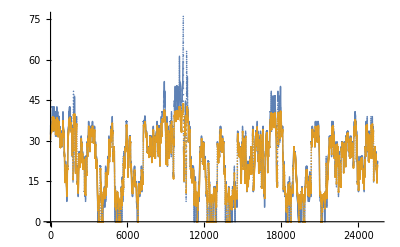

```mathematica
ListPlot[{testdata[[All,2]],tvalues}]
```

```mathematica
sobj=NetStateObject[trainedNet]
```

NetStateObject[<>]

```mathematica
NestList[sobj[{#}]&,testdata[[1,1]],8]
```

NetStateObject::invindata1: Data supplied to port "Input" was a 1×1 matrix, but expected a n×10 matrix.

NetStateObject::invindata2: Data supplied to port "Input" was not a n×10 matrix.

General::stop: Further output of NetStateObject::invindata2 will be suppressed during this calculation.

{{{29.52,29.808,30.096,30.384,30.672,30.96,31.248,31.536,31.824,32.112}},{29.6887},$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
results=Union@Flatten@NestList[Drop[Join[#,{trainedNet[#]}],1]&,testdata[[1,1]],100]
```

{29.52,29.808,30.096,30.384,30.672,30.96,31.248,31.536,31.824,32.112,32.4739,32.7695,33.0625,33.3513,33.6347,33.9169,34.1959,34.4704,34.7422,35.0063,35.2681,35.5172,35.7594,35.9947,36.2229,36.4441,36.6581,36.8644,37.0634,37.2544,37.438,37.6135,37.7817,37.9425,38.0962,38.243,38.3828,38.5159,38.6426,38.7628,38.877,38.9853,39.0879,39.1851,39.277,39.364,39.4461,39.5237,39.5969,39.666,39.7311,39.7925,39.8502,39.9046,39.9558,40.004,40.0492,40.0918,40.1318,40.1693,40.2046,40.2377,40.2687,40.2979,40.3252,40.3509,40.375,40.3975,40.4187,40.4385,40.457,40.4744,40.4907,40.506,40.5203,40.5337,40.5462,40.5579,40.5689,40.5792,40.5888,40.5979,40.6063,40.6142,40.6216,40.6285,40.635,40.641,40.6467,40.652,40.6569,40.6616,40.6659,40.67,40.6737,40.6773,40.6806,40.6837,40.6866,40.6893,40.6919,40.6943,40.6965,40.6986,40.7005,40.7023,40.704,40.7056,40.7071,40.7085}

```mathematica
ListPlot[{testdata[[1;;1000,2]],results}]
```

-Graphics-

```mathematica
ResourceObject["Museum of Modern Art Holdings and Artists"]["ContentTypes"]
```

{Entity Store}

```mathematica
ResourceObject["Meteorite Landings"]
```

ResourceObject[…]

```mathematica
Table[i,{i,0,360,30}]
```

{0,30,60,90,120,150,180,210,240,270,300,330,360}

```mathematica
l={-0.102754,0.292103,-1.70704,1.43537,-0.698093,-0.468061,-0.292096,-0.452018,0.391917,-0.573215,-0.378625,-0.464892,-0.338387,-0.670118,-0.393916,1.47693,0.0613546,-0.696489,-1.40548,-0.628233,-0.853413,-0.612489,-0.440041,-0.478317,-0.463197,-0.537035,-0.477848,1.81074,-0.475051,-0.230501,-0.234804,-1.19283,-0.501529,1.21399};
```

```mathematica
Mean@l
```

-0.267178